## Geometrical Spreading code for Multilayered VTI media_direct

```mathematica
Clear["Global`*"]
```

#### layer parameters

```mathematica
eta[1]=0.1
```

0.1

```mathematica
eta[2]=0.12
```

0.12

```mathematica
eta[3]=0.18
```

0.18

```mathematica
eta[4]=0.2
```

0.2

```mathematica
eta[5]=0.22
```

0.22

```mathematica
v0[1]=1.5;
v0[2]=1.8;
v0[3]=2;
v0[4]=2.2;
v0[5]=2.5;
```

```mathematica
vn[1]=1.7
vn[2]=2
vn[3]=2.3
vn[4]=2.5
vn[5]=2.8
```

1.7

2

2.3

2.5

2.8

### layer thickness

```mathematica
z0[1]=0.3;
z0[2]=0.7;
z0[3]=1;
z0[4]=1.5;
z0[5]=0.5;
```

```mathematica
T0=Sum[z0[i]/v0[i],{i,1,5}]
```

1.97071

```mathematica
VN=Sqrt[Sum[vn[i]^2*z0[i]/v0[i],{i,1,5}]/T0]
```

2.32009

```mathematica
ETA=((Sum[(1+8*eta[i])*vn[i]^4*z0[i]/v0[i],{i,1,5}]/(T0*VN^4))-1)/8
```

0.208884

#### Multilayered model effeective V0,Vn,ETA

```mathematica
Xp=Sum[(p vn[i]^2 z0[i])/(v0[i] (1-2 p^2 eta[i] vn[i]^2)^(3/2) √(1-p^2 (1+2 eta[i]) vn[i]^2)),{i,1,5}];
```

```mathematica
Lid0=(√2)/(√((((2 Xp)/VN^2+(4 ETA Xp^4 ((2 Bo Xp)/VN^2+((4 Bo T0^2 Xp)/VN^2+(4 Co Xp^3)/VN^4)/(2 √(T0^4+(2 Bo T0^2 Xp^2)/VN^2+(Co Xp^4)/VN^4))))/(VN^4 (T0^2+(Bo Xp^2)/VN^2+√(T0^4+(2 Bo T0^2 Xp^2)/VN^2+(Co Xp^4)/VN^4))^2)-(16 ETA Xp^3)/(VN^4 (T0^2+(Bo Xp^2)/VN^2+√(T0^4+(2 Bo T0^2 Xp^2)/VN^2+(Co Xp^4)/VN^4)))) (-(((2 Xp)/VN^2+(4 ETA Xp^4 ((2 Bo Xp)/VN^2+((4 Bo T0^2 Xp)/VN^2+(4 Co Xp^3)/VN^4)/(2 √(T0^4+(2 Bo T0^2 Xp^2)/VN^2+(Co Xp^4)/VN^4))))/(VN^4 (T0^2+(Bo Xp^2)/VN^2+√(T0^4+(2 Bo T0^2 Xp^2)/VN^2+(Co Xp^4)/VN^4))^2)-(16 ETA Xp^3)/(VN^4 (T0^2+(Bo Xp^2)/VN^2+√(T0^4+(2 Bo T0^2 Xp^2)/VN^2+(Co Xp^4)/VN^4))))^2)/(4 (T0^2+Xp^2/VN^2-(4 ETA Xp^4)/(VN^4 (T0^2+(Bo Xp^2)/VN^2+√(T0^4+(2 Bo T0^2 Xp^2)/VN^2+(Co Xp^4)/VN^4))))^(3/2))+(2/VN^2-(8 ETA Xp^4 ((2 Bo Xp)/VN^2+((4 Bo T0^2 Xp)/VN^2+(4 Co Xp^3)/VN^4)/(2 √(T0^4+(2 Bo T0^2 Xp^2)/VN^2+(Co Xp^4)/VN^4)))^2)/(VN^4 (T0^2+(Bo Xp^2)/VN^2+√(T0^4+(2 Bo T0^2 Xp^2)/VN^2+(Co Xp^4)/VN^4))^3)+(4 ETA Xp^4 ((2 Bo)/VN^2-(((4 Bo T0^2 Xp)/VN^2+(4 Co Xp^3)/VN^4)^2)/(4 (T0^4+(2 Bo T0^2 Xp^2)/VN^2+(Co Xp^4)/VN^4)^(3/2))+((4 Bo T0^2)/VN^2+(12 Co Xp^2)/VN^4)/(2 √(T0^4+(2 Bo T0^2 Xp^2)/VN^2+(Co Xp^4)/VN^4))))/(VN^4 (T0^2+(Bo Xp^2)/VN^2+√(T0^4+(2 Bo T0^2 Xp^2)/VN^2+(Co Xp^4)/VN^4))^2)+(32 ETA Xp^3 ((2 Bo Xp)/VN^2+((4 Bo T0^2 Xp)/VN^2+(4 Co Xp^3)/VN^4)/(2 √(T0^4+(2 Bo T0^2 Xp^2)/VN^2+(Co Xp^4)/VN^4))))/(VN^4 (T0^2+(Bo Xp^2)/VN^2+√(T0^4+(2 Bo T0^2 Xp^2)/VN^2+(Co Xp^4)/VN^4))^2)-(48 ETA Xp^2)/(VN^4 (T0^2+(Bo Xp^2)/VN^2+√(T0^4+(2 Bo T0^2 Xp^2)/VN^2+(Co Xp^4)/VN^4))))/(2 √(T0^2+Xp^2/VN^2-(4 ETA Xp^4)/(VN^4 (T0^2+(Bo Xp^2)/VN^2+√(T0^4+(2 Bo T0^2 Xp^2)/VN^2+(Co Xp^4)/VN^4)))))))/(Xp √(T0^2+Xp^2/VN^2-(4 ETA Xp^4)/(VN^4 (T0^2+(Bo Xp^2)/VN^2+√(T0^4+(2 Bo T0^2 Xp^2)/VN^2+(Co Xp^4)/VN^4)))))))/.Bo->2.0756423492037994/.Co->-0.26281746235037584;
```

```mathematica
Lid1=((√2)/(√((((2 Xp)/VN^2+(4 ETA Xp^4 ((2 (1+8 ETA+8 ETA^2) Xp)/((1+2 ETA) VN^2)+((4 (1+8 ETA+8 ETA^2) T0^2 Xp)/((1+2 ETA) VN^2)+(4 Xp^3)/((1+2 ETA)^2 VN^4))/(2 √(T0^4+(2 (1+8 ETA+8 ETA^2) T0^2 Xp^2)/((1+2 ETA) VN^2)+Xp^4/((1+2 ETA)^2 VN^4)))))/(VN^4 (T0^2+((1+8 ETA+8 ETA^2) Xp^2)/((1+2 ETA) VN^2)+√(T0^4+(2 (1+8 ETA+8 ETA^2) T0^2 Xp^2)/((1+2 ETA) VN^2)+Xp^4/((1+2 ETA)^2 VN^4)))^2)-(16 ETA Xp^3)/(VN^4 (T0^2+((1+8 ETA+8 ETA^2) Xp^2)/((1+2 ETA) VN^2)+√(T0^4+(2 (1+8 ETA+8 ETA^2) T0^2 Xp^2)/((1+2 ETA) VN^2)+Xp^4/((1+2 ETA)^2 VN^4))))) (-(((2 Xp)/VN^2+(4 ETA Xp^4 ((2 (1+8 ETA+8 ETA^2) Xp)/((1+2 ETA) VN^2)+((4 (1+8 ETA+8 ETA^2) T0^2 Xp)/((1+2 ETA) VN^2)+(4 Xp^3)/((1+2 ETA)^2 VN^4))/(2 √(T0^4+(2 (1+8 ETA+8 ETA^2) T0^2 Xp^2)/((1+2 ETA) VN^2)+Xp^4/((1+2 ETA)^2 VN^4)))))/(VN^4 (T0^2+((1+8 ETA+8 ETA^2) Xp^2)/((1+2 ETA) VN^2)+√(T0^4+(2 (1+8 ETA+8 ETA^2) T0^2 Xp^2)/((1+2 ETA) VN^2)+Xp^4/((1+2 ETA)^2 VN^4)))^2)-(16 ETA Xp^3)/(VN^4 (T0^2+((1+8 ETA+8 ETA^2) Xp^2)/((1+2 ETA) VN^2)+√(T0^4+(2 (1+8 ETA+8 ETA^2) T0^2 Xp^2)/((1+2 ETA) VN^2)+Xp^4/((1+2 ETA)^2 VN^4)))))^2)/(4 (T0^2+Xp^2/VN^2-(4 ETA Xp^4)/(VN^4 (T0^2+((1+8 ETA+8 ETA^2) Xp^2)/((1+2 ETA) VN^2)+√(T0^4+(2 (1+8 ETA+8 ETA^2) T0^2 Xp^2)/((1+2 ETA) VN^2)+Xp^4/((1+2 ETA)^2 VN^4)))))^(3/2))+(2/VN^2-(8 ETA Xp^4 ((2 (1+8 ETA+8 ETA^2) Xp)/((1+2 ETA) VN^2)+((4 (1+8 ETA+8 ETA^2) T0^2 Xp)/((1+2 ETA) VN^2)+(4 Xp^3)/((1+2 ETA)^2 VN^4))/(2 √(T0^4+(2 (1+8 ETA+8 ETA^2) T0^2 Xp^2)/((1+2 ETA) VN^2)+Xp^4/((1+2 ETA)^2 VN^4))))^2)/(VN^4 (T0^2+((1+8 ETA+8 ETA^2) Xp^2)/((1+2 ETA) VN^2)+√(T0^4+(2 (1+8 ETA+8 ETA^2) T0^2 Xp^2)/((1+2 ETA) VN^2)+Xp^4/((1+2 ETA)^2 VN^4)))^3)+(4 ETA Xp^4 ((2 (1+8 ETA+8 ETA^2))/((1+2 ETA) VN^2)-(((4 (1+8 ETA+8 ETA^2) T0^2 Xp)/((1+2 ETA) VN^2)+(4 Xp^3)/((1+2 ETA)^2 VN^4))^2)/(4 (T0^4+(2 (1+8 ETA+8 ETA^2) T0^2 Xp^2)/((1+2 ETA) VN^2)+Xp^4/((1+2 ETA)^2 VN^4))^(3/2))+((4 (1+8 ETA+8 ETA^2) T0^2)/((1+2 ETA) VN^2)+(12 Xp^2)/((1+2 ETA)^2 VN^4))/(2 √(T0^4+(2 (1+8 ETA+8 ETA^2) T0^2 Xp^2)/((1+2 ETA) VN^2)+Xp^4/((1+2 ETA)^2 VN^4)))))/(VN^4 (T0^2+((1+8 ETA+8 ETA^2) Xp^2)/((1+2 ETA) VN^2)+√(T0^4+(2 (1+8 ETA+8 ETA^2) T0^2 Xp^2)/((1+2 ETA) VN^2)+Xp^4/((1+2 ETA)^2 VN^4)))^2)+(32 ETA Xp^3 ((2 (1+8 ETA+8 ETA^2) Xp)/((1+2 ETA) VN^2)+((4 (1+8 ETA+8 ETA^2) T0^2 Xp)/((1+2 ETA) VN^2)+(4 Xp^3)/((1+2 ETA)^2 VN^4))/(2 √(T0^4+(2 (1+8 ETA+8 ETA^2) T0^2 Xp^2)/((1+2 ETA) VN^2)+Xp^4/((1+2 ETA)^2 VN^4)))))/(VN^4 (T0^2+((1+8 ETA+8 ETA^2) Xp^2)/((1+2 ETA) VN^2)+√(T0^4+(2 (1+8 ETA+8 ETA^2) T0^2 Xp^2)/((1+2 ETA) VN^2)+Xp^4/((1+2 ETA)^2 VN^4)))^2)-(48 ETA Xp^2)/(VN^4 (T0^2+((1+8 ETA+8 ETA^2) Xp^2)/((1+2 ETA) VN^2)+√(T0^4+(2 (1+8 ETA+8 ETA^2) T0^2 Xp^2)/((1+2 ETA) VN^2)+Xp^4/((1+2 ETA)^2 VN^4)))))/(2 √(T0^2+Xp^2/VN^2-(4 ETA Xp^4)/(VN^4 (T0^2+((1+8 ETA+8 ETA^2) Xp^2)/((1+2 ETA) VN^2)+√(T0^4+(2 (1+8 ETA+8 ETA^2) T0^2 Xp^2)/((1+2 ETA) VN^2)+Xp^4/((1+2 ETA)^2 VN^4))))))))/(Xp √(T0^2+Xp^2/VN^2-(4 ETA Xp^4)/(VN^4 (T0^2+((1+8 ETA+8 ETA^2) Xp^2)/((1+2 ETA) VN^2)+√(T0^4+(2 (1+8 ETA+8 ETA^2) T0^2 Xp^2)/((1+2 ETA) VN^2)+Xp^4/((1+2 ETA)^2 VN^4)))))))));
```

## GMA_limit

```mathematica
AA0=T0 VN^2;
AA2=-(-1-8 ETA)/T0;
AA4=-(9 (ETA+4 ETA^2))/(T0^3 VN^2);
```

```mathematica
GS1=33.192408127668266;
```

```mathematica
DGS1=7.8943101921004715;
```

```mathematica
BB2=-(2 AA4 X^2)/(AA0-GS1+AA2 X^2)-(DGS1-2 AA2 X)/(2 AA0 X-2 GS1 X+DGS1 X^2)/.X->5;
```

```mathematica
BB4=(DGS1-2 AA2 X)^2/(X^2 (2 AA0-2 GS1+DGS1 X)^2)+(4 AA4)/(AA0-GS1+AA2 X^2)/.X->5;
```

```mathematica
Ld0=AA0+AA2 Xp^2+(2 AA4 Xp^4)/(1+BB2 Xp^2+√(1+2 BB2 Xp^2+BB4 Xp^4));
```

## GMA

```mathematica
Ld1=T0 VN^2-((-1-8 ETA) Xp^2)/T0-(18 (ETA+4 ETA^2) Xp^4)/(T0^3 VN^2 (1+(((-1-8 ETA)^2/T0^2+(2 (-1-8 ETA) √(1/(1+2 ETA)))/T0^2+1/((1+2 ETA) T0^2)+(18 (ETA+4 ETA^2))/T0^2-(18 (1+6 ETA) (ETA+4 ETA^2))/((1/(1+2 ETA))^(3/2) T0^2)) Xp^2)/((-(-1-8 ETA)/T0-(√(1/(1+2 ETA)))/T0) (T0 VN^2-((1+6 ETA) T0 VN^2)/(1/(1+2 ETA))^(3/2)))+√(1+(2 ((-1-8 ETA)^2/T0^2+(2 (-1-8 ETA) √(1/(1+2 ETA)))/T0^2+1/((1+2 ETA) T0^2)+(18 (ETA+4 ETA^2))/T0^2-(18 (1+6 ETA) (ETA+4 ETA^2))/((1/(1+2 ETA))^(3/2) T0^2)) Xp^2)/((-(-1-8 ETA)/T0-(√(1/(1+2 ETA)))/T0) (T0 VN^2-((1+6 ETA) T0 VN^2)/(1/(1+2 ETA))^(3/2)))+((-(-1-8 ETA)/T0-(√(1/(1+2 ETA)))/T0)^2 Xp^4)/((T0 VN^2-((1+6 ETA) T0 VN^2)/(1/(1+2 ETA))^(3/2))^2))));
```

## exact

```mathematica
L33=Sum[(vn[i]^2 √(1+4 p^2 eta[i] vn[i]^2-6 p^4 eta[i] vn[i]^4-12 p^4 eta[i]^2 vn[i]^4) z0[i])/(v0[i] (1-2 p^2 eta[i] vn[i]^2)^2 (1-p^2 (1+2 eta[i]) vn[i]^2)),{i,1,5}];
```

#### relative errors

```mathematica
pp1=Abs[(L33-Lid0)]*100/L33;
pp2=Abs[(L33-Lid1)]*100/L33;
pp22=Abs[(L33-Ld0)]*100/L33;
pp3=Abs[(L33-Ld1)]*100/L33;
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

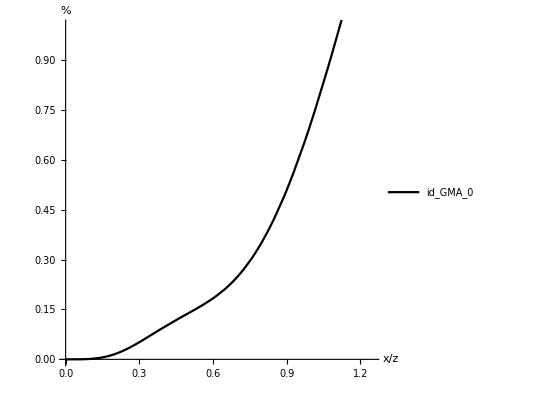
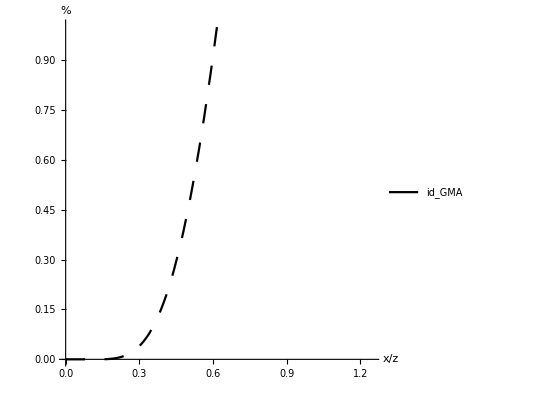
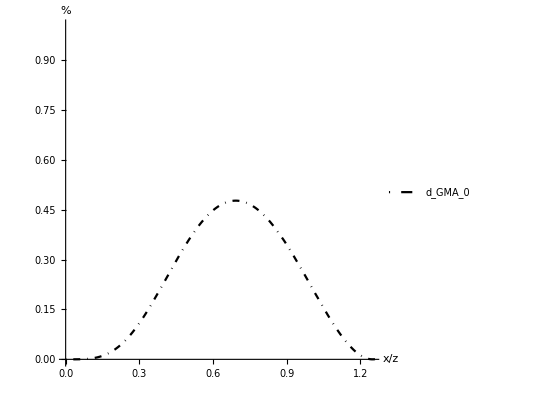
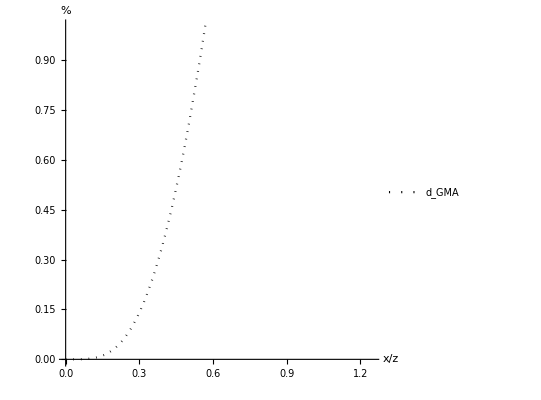

```mathematica
{a00=ParametricPlot[{Xp/4,pp1},{p,0,0.9},PlotStyle->{Directive[Black,Thick]},AspectRatio->1,PlotRange->{{0,1.25},{0,1}},AxesLabel->{Style["x/z",FontSize->20],Style["%",FontSize->20]},PlotLegends->Placed[{"id_GMA_0"},Right]],
a01=ParametricPlot[{Xp/4,pp2},{p,0,0.9},PlotStyle->{Directive[Dashing[Large],Black,Thick]},AspectRatio->1,PlotRange->{{0,1.25},{0,1}},AxesLabel->{Style["x/z",FontSize->20],Style["%",FontSize->20]},PlotLegends->Placed[{"id_GMA"},Right]],a012=ParametricPlot[{Xp/4,pp22},{p,0,0.9},PlotStyle->{Directive[DotDashed,Black,Thick]},AspectRatio->1,PlotRange->{{0,1.25},{0,1}},AxesLabel->{Style["x/z",FontSize->20],Style["%",FontSize->20]},PlotLegends->Placed[{"d_GMA_0"},Right]],
a02=ParametricPlot[{Xp/4,pp3},{p,0,0.9},PlotStyle->{Directive[Dotted,Black,Thick]},AspectRatio->1,PlotRange->{{0,1.25},{0,1}},AxesLabel->{Style["x/z",FontSize->20],Style["%",FontSize->20]},PlotLegends->Placed[{"d_GMA"},Right]]}
```

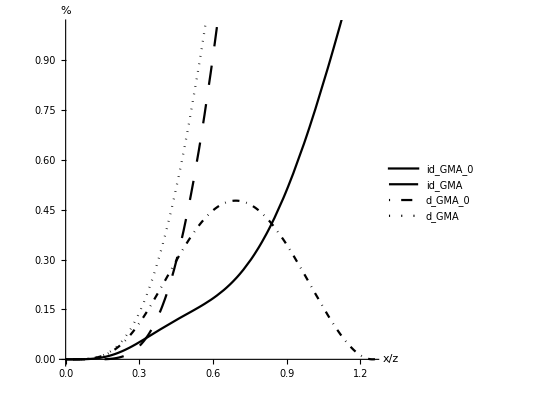

```mathematica
Show[a00,a01,a012,a02]
```